# Brian Martin ES 288 Midterm

```mathematica
IndicatorSentiment = {-0.20000000298023224,0,0,0,-0.20000000298023224,0.20000000298023224,0,-0.10000000149011612,0.10000000149011612,-0.10000000149011612,0,0,0,0,0,-0.30000001192092896,0}
```

```mathematica
SadFace=ImageResize[Import["C:\\Users\\Brian\\Downloads\\SadFace.png","PNG"],86];
NeutralFace=ImageResize[Import["C:\\Users\\Brian\\Downloads\\NeutralFace.png","PNG"],86];
HappyFace=ImageResize[Import["C:\\Users\\Brian\\Downloads\\HappyFace.png","PNG"],90];
```

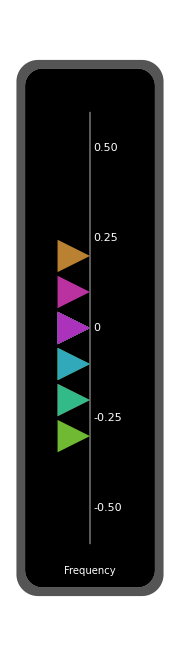

```mathematica
VerticalGauge[IndicatorSentiment, {-0.6, 0.6}, 
 GaugeMarkers -> Placed["Bar", "Scale"], GaugeFaceStyle -> Black, 
 GaugeFrameStyle -> Darker@Gray,  
 ScaleDivisions -> 5, GaugeLabels -> Placed["Frequency", Bottom],
 AxesStyle -> Gray, LabelStyle -> Directive[White],ScaleDivisions->6]
```

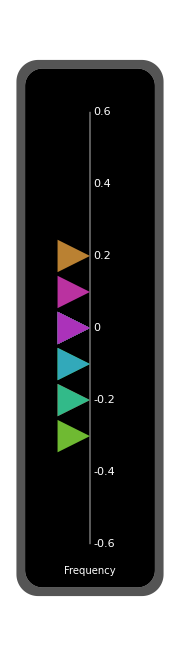

```mathematica
VerticalGauge[IndicatorSentiment,{-0.6,0.6},GaugeMarkers->Placed["Bar","Scale"],GaugeFaceStyle->Black,GaugeFrameStyle->Darker[Gray],GaugeLabels->Placed["Frequency",Bottom],AxesStyle->Gray,LabelStyle->Directive[White],ScaleDivisions->6]
```

```mathematica
face[x_]:=Which[IndicatorSentiment[[x]]>0,HappyFace,IndicatorSentiment[[x]] == 0, NeutralFace, IndicatorSentiment[[x]]<1,SadFace]
```

```mathematica
Manipulate[GraphicsRow[{VerticalGauge[IndicatorSentiment[[SDG]],{-0.6,0.6},GaugeMarkers->Placed["Bar","Scale"],GaugeFaceStyle->Black,GaugeFrameStyle->Darker[Gray],ScaleDivisions->5,GaugeLabels->Placed["Frequency",Bottom],AxesStyle->Gray,LabelStyle->Directive[White]],face[SDG]}],{SDG,1,Length[IndicatorSentiment],1}]
```

```mathematica
Manipulate[AngularGauge[IndicatorSentiment[[SDG]],{-1,1},PlotTheme->{"Minimal","GaugeHalf"},GaugeStyle ->{RGBColor[255,105,98],LightRed}],{SDG,1,Length[IndicatorSentiment],1}]
```